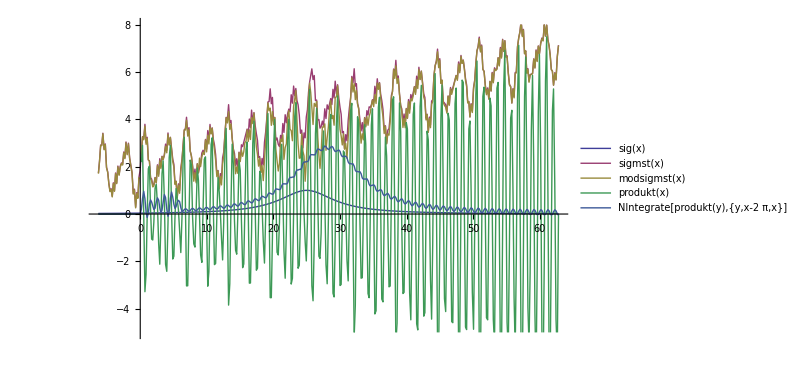

```mathematica
refsig[x_]=Sin[6x]*UnitStep[x];
sig[x_]=1/(1+(0.2x-5)^2);
stö[x_]=2+0.05x+0.0005 x^2+Sin[2x]+0.5Sin[3x]+0.3Sin[20x];
sigmst[x_]=sig[x]+stö[x];
modsigmst[x_]=refsig[x]*sig[x]+stö[x];
produkt[x_]=modsigmst[x]*refsig[x];

Plot[
{sig[x],sigmst[x],modsigmst[x],produkt[x],NIntegrate[produkt[y],{y,x-2π,x}]},
{x,-2π,2π *10},
PlotRange->{-5,8},
PlotPoints->100,
ImageSize->600,
MaxRecursion->2,
PlotLegends->"Expressions"
]
```